```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts"]
```

C:\Users\pglpm\repositories\genobayes\scripts

```mathematica
nn=5*10^6;
```

```mathematica
data=Import["dataset1_simple.csv"];
n=Length[data[[;;,1]]];
Dimensions[data]
```

{6029,97}

```mathematica
tally[sym_,gen_]:=SortBy[Tally[data[[;;,Join[Flatten@{sym},Flatten@{3+gen}]]]],FromDigits[#[[1]],2]&];
labels[sym_,gen_]:=
ArrayReshape[tally[sym,gen][[;;,1]],{2^Length@Flatten@{sym},2^Length@Flatten@{gen},Length@Flatten@{sym,gen}}];ClearAll[fs];fs[sym_,gen_]:=fs[sym,gen]=
ArrayReshape[tally[sym,gen][[;;,2]]/n,{2^Length@Flatten@{sym},2^Length@Flatten@{gen}}];
ClearAll[fg];
fg[gen_]:=tally[{},gen][[;;,2]]/n;
ClearAll[fc];fc[sym_,gen_]:=fc[sym,gen]=T[T[fs[sym,gen]]/fg[gen]];
```

```mathematica
stdf[f_]:=Sqrt[f*(1-f)/(n+1)];SetAttributes[stdf,Listable]
```

```mathematica
ClearAll[table];
table[sym_]:=table[sym]=Table[f=fc[sym,gene][[2]];{f,stdf[f]},{gene,94}]
```

```mathematica
tab2=SortBy[table[1][[;;,;;,2]],First];
ord2=Ordering[table[1][[;;,1,2]]];
tab2p=tab2[[;;,1]]+tab2[[;;,2]];
tab2m=tab2[[;;,1]]-tab2[[;;,2]];
```

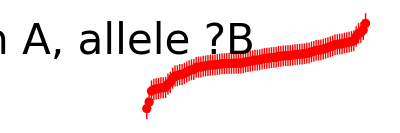

```mathematica
ErrorListPlot[tab2,Joined->False,PlotRange->{0.69,0.75},AspectRatio->1/3,Frame->Auto,Axes->None,FrameLabel->{Style[gene,41],Style[freq[symptom|"gene allele"],41]},PlotStyle->Red,FrameTicks->{Auto,{T@{Range[94],Style[#,15]&/@(ToString/@ord2)},None}},GridLines->Auto,ImageSize->a4longside*{3,1},Epilog->Text[Style["symptom A, allele ?B",42],Sequence@@labelposition[{0.5,0.9}]]]
```

```mathematica
Export["test_conditional_freqs_sA_aB.pdf",%]
```

test_conditional_freqs_sA_aB.pdf

```mathematica
ClearAll[sorttable,ordtable];sorttable[sym_,alle_]:=SortBy[table[sym][[;;,;;,alle]],First];
ordtable[sym_,alle_]:=Ordering[table[sym][[;;,1,alle]]];
```

```mathematica
symptoms={"A","B","C"};alleles={"AA","B"};
```

```mathematica
Do[plot=ErrorListPlot[Evaluate[sorttable[symx,allex]],Joined->False,PlotRange->All,AspectRatio->1/3,Frame->Auto,Axes->None,FrameLabel->{Style[gene,41],Style[freq[symptom|"gene allele"],41]},PlotStyle->{blue,red}[[allex]],FrameTicks->{Auto,{T@{Range[94],Style[#,15]&/@(ToString/@ordtable[symx,allex])},None}},GridLines->Auto,ImageSize->a4longside*{3,1},Epilog->Text[Style["symptom "<>symptoms[[symx]]<>", allele "<>alleles[[allex]],42],Sequence@@labelposition[{0.5,0.9}]]];
Export["test_conditional_freqs_s"<>symptoms[[symx]]<>"_a"<>alleles[[allex]]<>".pdf",plot]
,{symx,3},{allex,2}];
```

```mathematica
Export["test_conditional_freqs_sA_aB.pdf",%]
```

test_conditional_freqs_sA_aB.pdf

```mathematica
tab1=SortBy[table[1][[;;,;;,1]],First];
ord1=Ordering[table[1][[;;,1,1]]];
tab1p=tab1[[;;,1]]+tab1[[;;,2]];
tab1m=tab1[[;;,1]]-tab1[[;;,2]];
tab2=table[1][[;;,;;,2]][[ord1]];
(*ord2=Ordering[table[1][[;;,1,1]]];*)
tab2p=tab2[[;;,1]]+tab2[[;;,2]];
tab2m=tab2[[;;,1]]-tab2[[;;,2]];
```

```mathematica
Needs["ErrorBarPlots`"];
```

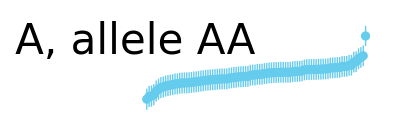

```mathematica
ErrorListPlot[tab1,Joined->False,PlotRange->{0.7,0.76},AspectRatio->1/3,Frame->Auto,Axes->None,FrameLabel->{Style[gene,41],Style[freq[symptom|"gene allele"],41]},FrameTicks->{Auto,{T@{Range[94],Style[#,15]&/@(ToString/@ord1)},None}},GridLines->Auto,ImageSize->a4longside*{3,1},Epilog->Text[Style["symptom A, allele AA",42],Sequence@@labelposition[{0.5,0.9}]]]
```

```mathematica
Export["test_conditional_freqs_sA_aAA.pdf",%]
```

test_conditional_freqs_sA_aAA.pdf

```mathematica
table[1]//N//MF
```

((0.732422
0.700402) | (0.00570095
0.00589908)
(0.725723
0.723506) | (0.00574542
0.00575977)
(0.718684
0.734188) | (0.00579039
0.00568895)
(0.721532
0.727392) | (0.00577241
0.00573449)
(0.728474
0.708263) | (0.00572735
0.00585375)
(0.746848
0.713544) | (0.00559948
0.00582211)
(0.729244
0.721834) | (0.00572225
0.00577048)
(0.734979
0.711286) | (0.00568354
0.00583576)
(0.726744
0.707317) | (0.00573874
0.00585932)
(0.726489
0.72315) | (0.00574042
0.00576206)
(0.728105
0.706468) | (0.00572979
0.00586429)
(0.727533
0.717615) | (0.00573356
0.00579706)
(0.728642
0.696815) | (0.00572624
0.00591907)
(0.729359
0.720553) | (0.00572148
0.00577862)
(0.727229
0.718363) | (0.00573556
0.0057924)
(0.725164
0.721095) | (0.00574906
0.00577518)
(0.716426
0.738309) | (0.00580444
0.0056605)
(0.726078
0.719562) | (0.0057431
0.00578487)
(0.732616
0.719737) | (0.00569964
0.00578377)
(0.727372
0.722087) | (0.00573462
0.00576887)
(0.727332
0.721545) | (0.00573489
0.00577232)
(0.72036
0.728027) | (0.00577984
0.00573031)
(0.726829
0.721717) | (0.00573819
0.00577123)
(0.724409
0.724651) | (0.00575394
0.00575238)
(0.721227
0.726833) | (0.00577435
0.00573816)
(0.730649
0.720875) | (0.00571288
0.00577658)
(0.729512
0.721285) | (0.00572047
0.00577398)
(0.720748
0.725921) | (0.00577738
0.00574413)
(0.729989
0.719702) | (0.00571729
0.00578399)
(0.728388
0.722956) | (0.00572792
0.00576331)
(0.723963
0.725873) | (0.00575683
0.00574444)
(0.721003
0.743784) | (0.00577577
0.0056217)
(0.713478
0.730484) | (0.00582252
0.00571399)
(0.719479
0.738716) | (0.00578539
0.00565766)
(0.711954
0.732057) | (0.00583174
0.00570341)
(0.722595
0.726552) | (0.00576562
0.00574)
(0.717452
0.729583) | (0.00579808
0.00571999)
(0.726702
0.722503) | (0.00573902
0.00576621)
(0.729254
0.721849) | (0.00572219
0.00577038)
(0.72715
0.708185) | (0.00573608
0.00585421)
(0.724323
0.725) | (0.0057545
0.00575012)
(0.735894
0.720147) | (0.00567725
0.00578119)
(0.729429
0.720271) | (0.00572102
0.0057804)
(0.72835
0.707855) | (0.00572818
0.00585616)
(0.726804
0.723699) | (0.00573835
0.00575853)
(0.730034
0.714932) | (0.00571699
0.00581364)
(0.728747
0.722707) | (0.00572555
0.0057649)
(0.725328
0.723512) | (0.00574798
0.00575973)
(0.724297
0.725118) | (0.00575467
0.00574935)
(0.724065
0.72608) | (0.00575617
0.00574309)
(0.713659
0.728401) | (0.00582141
0.00572784)
(0.722472
0.72742) | (0.00576641
0.00573431)
(0.723174
0.733506) | (0.00576191
0.0056936)
(0.723178
0.732477) | (0.00576188
0.00570058)
(0.722368
0.726691) | (0.00576707
0.00573909)
(0.723059
0.725581) | (0.00576264
0.00574634)
(0.719947
0.732175) | (0.00578245
0.00570262)
(0.721733
0.732974) | (0.00577112
0.00569721)
(0.725326
0.724113) | (0.005748
0.00575586)
(0.725739
0.718182) | (0.00574531
0.00579353)
(0.721455
0.725592) | (0.00577289
0.00574627)
(0.722984
0.727069) | (0.00576313
0.00573661)
(0.726531
0.710317) | (0.00574014
0.00584156)
(0.722738
0.728912) | (0.0057647
0.00572445)
(0.723516
0.72489) | (0.00575971
0.00575083)
(0.726241
0.721553) | (0.00574204
0.00577227)
(0.723775
0.729193) | (0.00575804
0.00572259)
(0.72446
0.724518) | (0.00575362
0.00575324)
(0.71976
0.736594) | (0.00578363
0.00567242)
(0.723135
0.726003) | (0.00576215
0.00574359)
(0.722137
0.740177) | (0.00576855
0.00564739)
(0.722768
0.733828) | (0.00576451
0.00569141)
(0.72454
0.724433) | (0.0057531
0.00575379)
(0.72567
0.716934) | (0.00574576
0.00580129)
(0.726828
0.716226) | (0.00573819
0.00580567)
(0.71921
0.729038) | (0.00578709
0.00572362)
(0.726643
0.721874) | (0.00573941
0.00577023)
(0.720892
0.729967) | (0.00577647
0.00571744)
(0.730068
0.714742) | (0.00571676
0.0058148)
(0.728305
0.715556) | (0.00572848
0.00580981)
(0.728305
0.715556) | (0.00572848
0.00580981)
(0.728398
0.708475) | (0.00572786
0.0058525)
(0.728625
0.707666) | (0.00572636
0.00585727)
(0.734308
0.72083) | (0.00568813
0.00577687)
(0.72198
0.726313) | (0.00576955
0.00574157)
(0.726829
0.721717) | (0.00573819
0.00577123)
(0.726829
0.721717) | (0.00573819
0.00577123)
(0.728512
0.720871) | (0.00572711
0.0057766)
(0.718355
0.730952) | (0.00579244
0.00571085)
(0.730708
0.721687) | (0.00571249
0.00577142)
(0.721046
0.732456) | (0.00577549
0.00570072)
(0.714461
0.731327) | (0.00581652
0.00570833)
(0.72042
0.726823) | (0.00577946
0.00573823)
(0.720952
0.733219) | (0.00577609
0.00569555))

```mathematica
fs[1,1]//N//MF
```

(0.551169 | 0.173329
0.20136 | 0.0741416)

```mathematica
fg[1]//N//MF
```

(0.752529
0.247471)

```mathematica
fc[1,1]//N//MF
```

(0.732422 | 0.700402
0.267578 | 0.299598)

```mathematica
fi=fs[{}]
```

{2427/6029,396/6029,1102/6029,443/6029,627/6029,73/6029,428/6029,533/6029}

```mathematica
listsample:=Block[{rsam=RandomSample[Range[94],25]},FoldList[Join,{rsam[[1]]},T@{rsam[[2;;]]}]]
```